```mathematica
ClearAll["Global`*"];
constToParam={aa->aConst,bb->bConst,cc->cConst,dd->dConst};
aConst=-t1e/t1n-(c α)/2-(c β)/2;
bConst=(c α)/2-(c β)/2;
cConst=α/2-β/2;
dConst=-1-α/2-β/2;
(* These correspond to coefficients in the decoupled equation for Subscript[P, n]
(a system of two linear first-order ODEs is transformed into a single linear second-order ODE) *)
simplToConst={aaa->aSimpl,bbb->bSimpl,ccc->cSimpl, pn0->pn0Simpl};
aSimpl=t1e^2/bb;
bSimpl=-t1e aa/bb-t1e dd/bb;
cSimpl=aa dd/bb-cc;
pn0Simpl=-bb/t1e;
eqnDecouple={aaa pn''[t]+bbb pn'[t]+ccc pn[t]+1==0,
pn[0]==0,pn'[0]==-bb/t1e};
eqnPe={t1e pe'[t]==cc pn[t]+dd pe[t]-1,
pe[t0]==pe0};
solPn=DSolve[eqnDecouple,pn[t],t][[1]];
(*solPe=DSolve[eqnPe/.solPn,pe[t],t];*)
pnSol[t]=pn[t]/.solPn;
(*peSol[t]=pe[t]/.solPe;*)
```

```mathematica
physicalTimes={t1e->0.03,t1n->25*60};
pnSol[t]/.simplToConst/.constToParam/.physicalTimes/.{α->0,β->5,c->0.0001}
```

-0.0310012 (-25.2006+0.00164575 ⅇ^(-116.673 t)+25.199 ⅇ^(-0.00304746 t))

```mathematica
eqnConst={t1e pn'[t]==aa pn[t]+bb pe[t],
t1e pe'[t]==cc pn[t]+dd pe[t]-1,
pn[0]==0,pe[0]==-1};
solConst=DSolve[eqnConst,{pn[t],pe[t]},t];
Plot[{pn[t],pe[t]}/.solConst/.constToParam/.physicalTimes/.{α->0,β->5,c->0.0001}//Simplify,{t,0,2000}]
```

-Graphics-

```mathematica
{pn[t],pe[t]}/.solConst/.constToParam/.physicalTimes/.{α->0,β->5,c->0.0001}
```

{{-0.00911011 ⅇ^(116.676 t) (0.00560039 ⅇ^(-233.348 t)+85.7508 ⅇ^(-116.679 t)-85.7564 ⅇ^(-116.676 t)+0.00223988 ⅇ^(-0.00609493 t)-0.00223988 ⅇ^(-0.00609493 t)),36.4404 ⅇ^(116.676 t) (-0.0196009 ⅇ^(-233.348 t)+0.015313 ⅇ^(-116.679 t)-0.0231542 ⅇ^(-116.676 t)+3.9999×10^-7 ⅇ^(-0.00609493 t)-3.9999×10^-7 ⅇ^(-0.00609493 t))}}

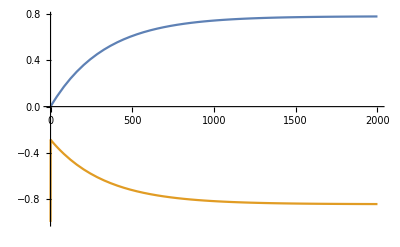

```mathematica
Plot[{-0.009110106613037811 ⅇ^(116.67566666666666 t) (0.00560039317903005 ⅇ^(-233.3482858697726 t)+85.75080545202508 ⅇ^(-116.67871413022738 t)-85.75640584520411 ⅇ^(-116.67566666666666 t)),
36.44042645215125 ⅇ^(116.67566666666666 t) (-0.019600864116776636 ⅇ^(-233.3482858697726 t)+0.015313043824516415 ⅇ^(-116.67871413022738 t)-0.023154229578205114 ⅇ^(-116.67566666666666 t))},
{t,0,2000}]
```

36.4404 ⅇ^(116.676 t) (-0.0196009 ⅇ^(-233.348 t)+0.015313 ⅇ^(-116.679 t)-0.0231542 ⅇ^(-116.676 t))

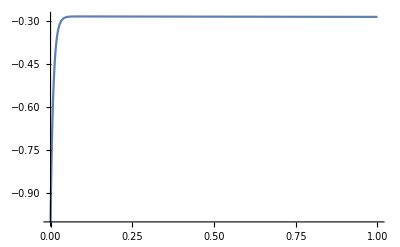

```mathematica
f[t_]=36.44042645215125 ⅇ^(116.67566666666666 t) (-0.019600864116776636 ⅇ^(-233.3482858697726 t)+0.015313043824516415 ⅇ^(-116.67871413022738 t)-0.023154229578205114 ⅇ^(-116.67566666666666 t))
Plot[f[t],{t,0,1},PlotRange->All]
```